```mathematica
Get["./workspace/wolfram/wikidataEntitystore.m"]
```

```mathematica
EntityUnregister["IrishHospital"]
EntityRegister@WikidataEntityStoreSparql["IrishHospital","?item wdt:P31/wdt:P279* wd:Q16917;
        wdt:P131 wd:Q1761."]
```

{IrishHospital}

```mathematica
EntityList["IrishHospital"]
```

{Beaumont Hospital, Dublin,Rotunda Hospital,Royal Victoria Eye and Ear Hospital,Central Remedial Clinic,Connolly Hospital,Coombe Women & Infants University Hospital,Mater Misericordiae University Hospital,Our Lady's Hospital for Sick Children in Crumlin,Mount Carmel Hospital,St. Michael's Hospital,St. Patrick's Hospital,St. James's Hospital,St. Vincent's University Hospital,Tallaght Hospital,National Maternity Hospital, Dublin,Central Mental Hospital,Phoenix Children's Hospital Ireland}

```mathematica
GeoListPlot@EntityList["IrishHospital"]
```

-Graphics-

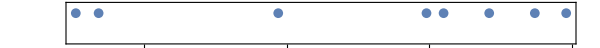

```mathematica
TimelinePlot[Values@EntityValue["IrishHospital","Inception","EntityAssociation"]]
```

```mathematica
EntityProperties["IrishHospital"]
```

{archon code,commons category,country,crossref funder id,encyclopædia britannica online id,freebase id,grid id,image,inception,instance of,isni,Label,located in the administrative territorial entity,microsoft academic id,official website,coordinate location,quora topic id,ringgold id,use,viaf id}

```mathematica
DeleteMissing@EntityValue["IrishHospital","Image"]
```

{-Graphics-,-Graphics-}

```mathematica
WikidataEntityStore["https://www.wikidata.org/wiki/Q179872"]
```

EntityStore[…]

```mathematica
EntityRegister@WikidataEntityStore["Q19546","P39"]
```

{Pope}

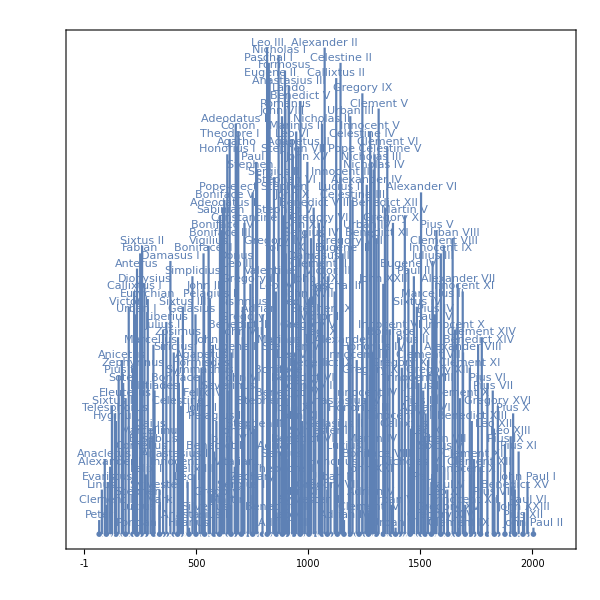

```mathematica
TimelinePlot[EntityValue[EntityList["Pope"],"DeathDate","EntityAssociation"]]
```

```mathematica
GeoHistogram[Interpreter["Country"][DeleteMissing@EntityValue[EntityList["Pope"],EntityProperty["Pope","CountryOfCitizenship"]]],"Country"]
```

-Graphics-